# Homework 10.4B

## Problem 1:

```mathematica
(*Graph and find the area of f(θ)*)
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
r = 9 + Sin[4θ];
```

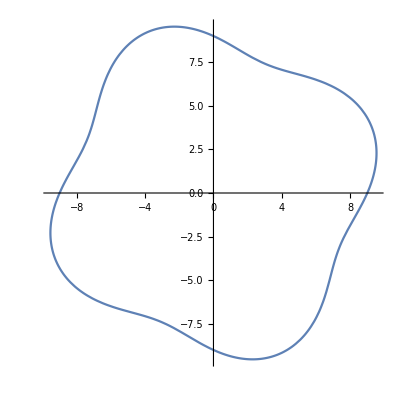

```mathematica
PolarPlot[r,{θ,0,2π}]
```

```mathematica
1/2*∫_0^(2π) r^2 ⅆθ
```

(163 π)/2

## Problem 2:

```mathematica
(*Graph and find the area of f(θ)*)
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
r = Sqrt[1 + (Cos[6θ])^2]
```

√(1+Cos[6 θ]^2)

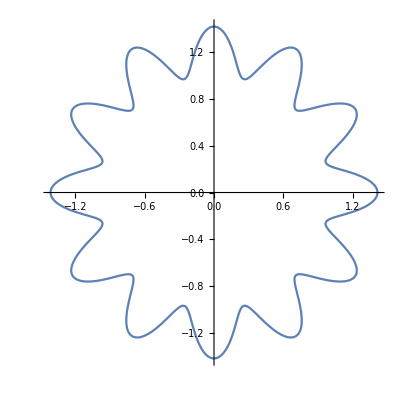

```mathematica
PolarPlot[r,{θ,0,2π}]
```

```mathematica
1/2*∫_0^(2π) r^2 ⅆθ
```

(3 π)/2

## Problem 3:

```mathematica
(* Find the area of the region enclosed by one loop of the curve.*)
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
r = 8*Sin[5*θ];
```

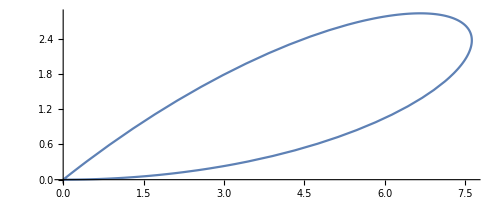

```mathematica
PolarPlot[r,{θ,0,π/5}]
```

```mathematica
1/2*∫_0^(π/5) r^2 ⅆθ
```

(16 π)/5

## Problem 4:

```mathematica
(*Find the area of the region that lies inside the first curve (crazy) and outside the second curve(circle) .*)
```

```mathematica
ClearAll["Global`*"]
```

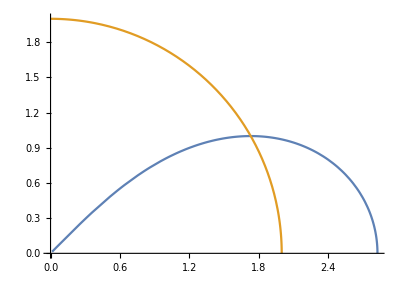

```mathematica
PolarPlot[{√(8*Cos[2θ]),2},{θ,0,π/2}]
```

```mathematica
(*Continued*)
```

## Problem 5:

```mathematica
(*Find the area of the region that lies inside the first curve and outside the second curve.*)
```

```mathematica
ClearAll["Global`*"]
```

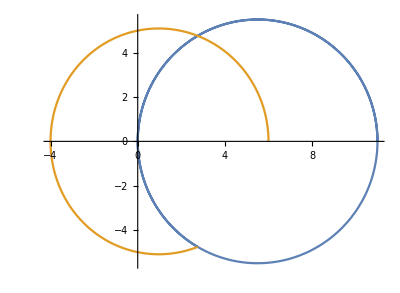

```mathematica
F[θ_] := 11*Cos[θ];
G[θ_] := 5+ Cos[θ];
PolarPlot[{F[θ]},{θ,0,5π/3}]
```

```mathematica
(*Find where the intersection points meet by adjusting the parameter using the unit circle,
1)For the first point it intersects π/3
2) For the second point it intersects at (5π)/3, but you want it to be less than π, so you just make it -π/3, because its an equal angle on the unit circle
3) You put the lower bound to the negative θ, and the larger θ as 'B'
1/2∫_α^β R^2-r^2 ⅆθ *)
```

```mathematica
1/2*∫_(-π/3)^(π/3) ((F[θ])^2-(G[θ])^2)ⅆθ
```

1/2 (20 √3+(70 π)/3)

## Problem 6:

```mathematica
(*Find the area of the region that lies inside both curves.*)
```

```mathematica
ClearAll["Gloabal`*"]
```

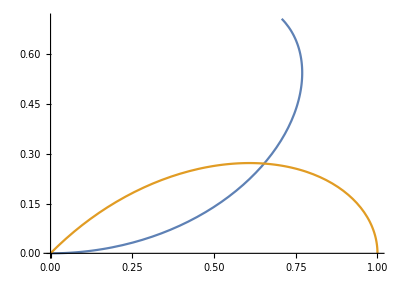

```mathematica
F[θ_]:= Sin[2θ];
G[θ_] := Cos[2θ];
PolarPlot[{F[θ],G[θ]},{θ,0,π/4}]
```

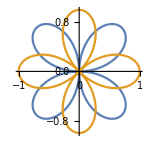

```mathematica
(* Sym_K = 8;
β= π/8;
α= π/4
```

```mathematica
8/2*∫_(π/8)^(π/4) ((G[θ])^2-(F[θ])^2)ⅆθ
```

-1

```mathematica
1/8*8
```

1